```mathematica
Symbolize[Subscript[L, arm]];
Symbolize[Subscript[d, p]];
Symbolize[x];
Symbolize[y];
Symbolize[Subscript[L, t]];
Symbolize[T];

Symbolize[Subscript[α, 1]];
Symbolize[Subscript[α, 2]];
```

```mathematica
Subscript[L, arm] = 0.25;
g = 9.8;
Subscript[m, s]=16.5;
Subscript[d, p] = 0.54;
Subscript[L, tval] = 1;
```

```mathematica
LTakeup[a_,b_, Larm_, dp_] := 4 Larm (Sin[a/2] + Sin[b/2]) - dp + Sqrt[(Larm (Sin[a] - Sin[b]))^2 + (Larm(2 - (Cos[a] + Cos[b])) + dp)^2 ];
```

```mathematica
Subscript[L, t] = LTakeup[a, b, Subscript[L, arm], Subscript[d, p]]
```

-0.54+1. (Sin[a/2]+Sin[b/2])+√((0.54+0.25 (2-Cos[a]-Cos[b]))^2+0.0625 (Sin[a]-Sin[b])^2)

```mathematica
Plot3D[Subscript[L, t],{a,0,2 Pi},{b,0,2 Pi}, AxesLabel->{Subscript[α, 1], Subscript[α, 2], Subscript[L, takeup]}]
```

-Graphics3D-

```mathematica
Subscript[L, t]
```

-0.54+1. (Sin[a/2]+Sin[b/2])+√((0.54+0.25 (2-Cos[a]-Cos[b]))^2+0.0625 (Sin[a]-Sin[b])^2)

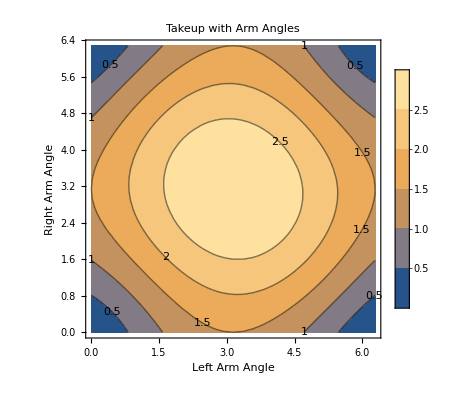

```mathematica
ContourPlot[Subscript[L, t], {a, 0, 2 * Pi}, {b, 0, 2 * Pi}, PlotLegends->Automatic, FrameLabel->{"Left Arm Angle","Right Arm Angle"}, PlotLabel -> "Takeup with Arm Angles", ContourLabels->(Text[Framed[#3],{#1,#2},BaseStyle->FontColor->Black]&)]
```

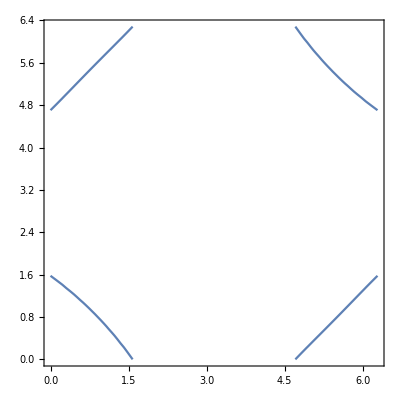

```mathematica
ContourPlot[Subscript[L, t]==Subscript[L, tval],{a,0, 2 Pi},{b,0,2 π}]
```

-((0.5 (0.54+0.25 (2-Cos[a]-Cos[b])) Sin[a]+0.125 Cos[a] (Sin[a]-Sin[b])) (-0.125 Cos[b] (Sin[a]-Sin[b])+0.5 (0.54+0.25 (2-Cos[a]-Cos[b])) Sin[b]))/(4 ((0.54+0.25 (2-Cos[a]-Cos[b]))^2+0.0625 (Sin[a]-Sin[b])^2)^(3/2))+(-0.125 Cos[a] Cos[b]+0.125 Sin[a] Sin[b])/(2 √((0.54+0.25 (2-Cos[a]-Cos[b]))^2+0.0625 (Sin[a]-Sin[b])^2))

-((0.5 (0.54+0.25 (2-Cos[a]-Cos[b])) Sin[a]+0.125 Cos[a] (Sin[a]-Sin[b])) (-0.125 Cos[b] (Sin[a]-Sin[b])+0.5 (0.54+0.25 (2-Cos[a]-Cos[b])) Sin[b]))/(4 ((0.54+0.25 (2-Cos[a]-Cos[b]))^2+0.0625 (Sin[a]-Sin[b])^2)^(3/2))+(-0.125 Cos[a] Cos[b]+0.125 Sin[a] Sin[b])/(2 √((0.54+0.25 (2-Cos[a]-Cos[b]))^2+0.0625 (Sin[a]-Sin[b])^2))

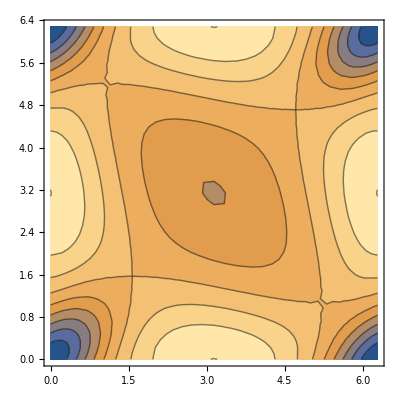

```mathematica
deriv = D[Subscript[L, t], a, b]
-(((0.5 (0.54+0.25 (2-Cos[a]-Cos[b])) Sin[a]+0.125 Cos[a] (Sin[a]-Sin[b])) (-0.125 Cos[b] (Sin[a]-Sin[b])+0.5 (0.54+0.25 (2-Cos[a]-Cos[b])) Sin[b]))/(4 ((0.54+0.25 (2-Cos[a]-Cos[b]))^2+0.0625 (Sin[a]-Sin[b])^2)^(3/2)))+(-0.125 Cos[a] Cos[b]+0.125 Sin[a] Sin[b])/(2 √((0.54+0.25 (2-Cos[a]-Cos[b]))^2+0.0625 (Sin[a]-Sin[b])^2))
ContourPlot[deriv, {a, 0, 2 * Pi}, {b, 0, 2 * Pi}]
```

```mathematica
Solve[Subscript[L, t]==Subscript[L, tval]/. a -> b][[3]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{b→ConditionalExpression[2. (0.427079+6.28319 C[1]), C[1]∈ℤ]}

```mathematica
Solve[Subscript[L, t]==1/. a -> 0, b][[1]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
{b->ConditionalExpression[2. (0.7890189984523611+6.283185307179586 C[1]), C[1]∈Integers]/. C = 0}
```

Set::write: Tag ReplaceAll in b→2./.C is Protected.

{0}

```mathematica
θ = 2 * 0.7890189984523611
```

1.57804

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of y→8.29156.

```mathematica
Symbolize[Subscript[L, ks]];
Symbolize[Subscript[L, c]];
Symbolize[Subscript[m, s]];
Symbolize[x];
Symbolize[y];
```

```mathematica
Subscript[L, ks] = 12.5;
Subscript[L, c] = 15;
Subscript[m, s]=16.5;
```

```mathematica
Solve[Sqrt[ys^2 + xs^2] + Sqrt[(2 (Subscript[L, ks]) - xs)^2 + ys^2] == 2 Subscript[L, c] - Subscript[L, tval] , ys][[2]]
```

{ys→√(13.8692+6.42093 xs-0.256837 xs^2)}

```mathematica
GetY[xs_]:=ys /.Solve[Sqrt[ys^2 + xs^2] + Sqrt[(2 (Subscript[L, ks]) - xs)^2 + ys^2] == 2 Subscript[L, c] - Subscript[L, tval] , ys][[2]];
GetY[2]
```

5.06791

```mathematica
LeftTensionAngle[y_, x_]:= ArcTan[y / x];
RightTensionAngle[y_, x_, Ls_] := ArcTan[y/(2Ls - x)];
Tension[Lc_,m_,Ls_] := m Lc g/(2Sqrt[Lc^2-Ls^2]);
DPLeverArm[ycg_, dp_]:= Sqrt[ycg^2 + dp^2];
TensionTorque[θ_, T_, r_, ycg_, dp_] := T r Sin[θ - ArcTan[ycg/(dp/2)]];
```

{y→√(21.0069+7.63889 x-0.305556 x^2)}

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {{y→-8.29156},{y→8.29156}}.

Hold[Solve[FullSimplify[√(y^2+x^2)+√((2 L_ks-x)^2+y^2)==2 L_c,y]]]

```mathematica
x = 2;
```

```mathematica
y = GetY[x]
```

5.06791

```mathematica
Subscript[τ, TL]=TensionTorque[LeftTensionAngle[y, x], Tension[Subscript[L, c]-1, Subscript[m, s], Subscript[L, ks]], DPLeverArm[0, Subscript[d, p]], 0, Subscript[d, p]]
```

90.1785

```mathematica
Subscript[τ, TR] = TensionTorque[RightTensionAngle[y, x, Subscript[L, ks]], Tension[Subscript[L, c]-1, Subscript[m, s], Subscript[L, ks]], DPLeverArm[0, Subscript[d, p]], 0, Subscript[d, p]]
```

20.8612

```mathematica
APLeverArm[α_, La_, ycg_, dp_ ]:= Sqrt[(La Sin[α] + ycg)^2 + (dp/2 + La(1 - Cos[α]))^2];
TempArmTorqueAngle[α_, La_, ycg_, dp_, r_]:= α + ArcSin[(La Sin[α] + ycg)/r];
LeftArmTorqueAngle[θ_] := θ - Pi / 2; 
RightArmTorqueAngle[θ_] := Pi/2 - θ;
MotorTorque[at_, La_, r_, θ_]:= (at * La)/(r Sin[θ]);
```

0.578604

```mathematica
Subscript[r, arm] = APLeverArm[θ, Subscript[L, arm], 0, Subscript[d, p]]
Subscript[θ, τr] = RightArmTorqueAngle[TempArmTorqueAngle[θ, Subscript[L, arm], 0, Subscript[d, p],  Subscript[r, arm]]]
MotorTorque[Subscript[τ, TL] - Subscript[τ, TR], Subscript[L, arm], Subscript[r, arm], Subscript[θ, τr]]
```

0.578604

-0.454021

-68.2887

```mathematica
TorqueApprox[xs_]:= MotorTorque[TensionTorque[LeftTensionAngle[GetY[xs], xs], Tension[Subscript[L, c]-1, Subscript[m, s], Subscript[L, ks]], DPLeverArm[0, Subscript[d, p]], 0, Subscript[d, p]] - TensionTorque[RightTensionAngle[GetY[xs], xs, Subscript[L, ks]], Tension[Subscript[L, c]-1, Subscript[m, s], Subscript[L, ks]], DPLeverArm[0, Subscript[d, p]], 0, Subscript[d, p]], Subscript[L, arm], Subscript[r, arm], LeftArmTorqueAngle[TempArmTorqueAngle[θ, Subscript[L, arm], 0, Subscript[d, p],  Subscript[r, arm]]]];
```

```mathematica
TorqueApprox[5]
```

46.1105

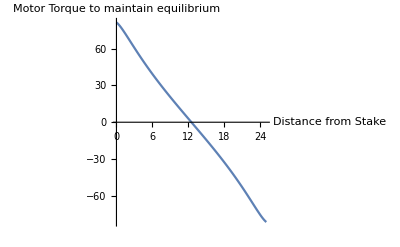

```mathematica
Plot[TorqueApprox[Subscript[x, s]], {Subscript[x, s], 0, 2 Subscript[L, ks]}, AxesLabel -> {"Distance from Stake", "Motor Torque to maintain equilibrium"}]
```

```mathematica
DiffInArm[θ_, La_, dp_]:= ArcTan[La Sin[θ]/(dp + La(1 - Cos[θ]))];
TorqueAroundMotor[θ_, diff_, TL_, TR_]:= (TL + TR)/2 * Sin[diff + θ] + TL * (Pi/2 - θ/2);
```

```mathematica
TorqueAroundMotor[θ, DiffInArm[θ, Subscript[L, arm], Subscript[d, p]], Tension[Subscript[L, c]-1, Subscript[m, s], Subscript[L, ks]], Tension[Subscript[L, c]-1, Subscript[m, s], Subscript[L, ks]]]
```

311.158

```mathematica
Tension[Subscript[L, c]-1, Subscript[m, s], Subscript[L, ks]]
```

179.531